### State transition diagrams

### In N Out Degree Distributions

These plot suck, they don't really tell us anything!

```mathematica
Clear["Global`*"]
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->1];
```

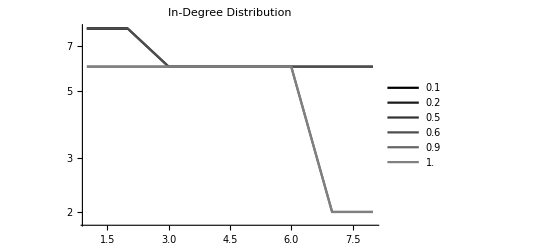
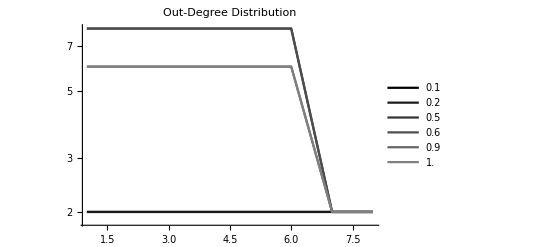
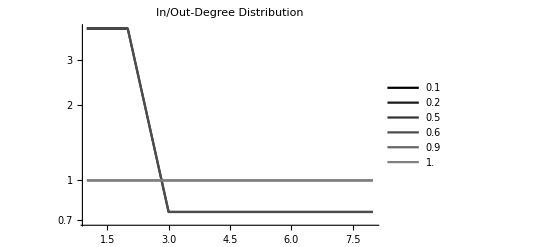
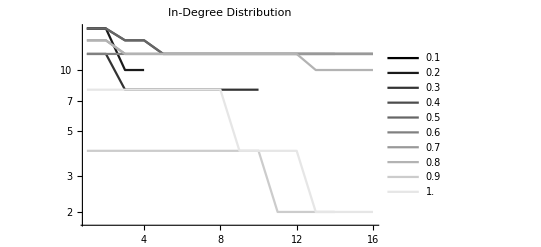
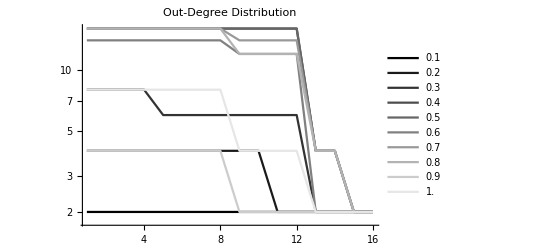
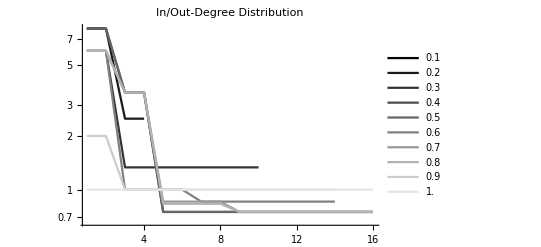
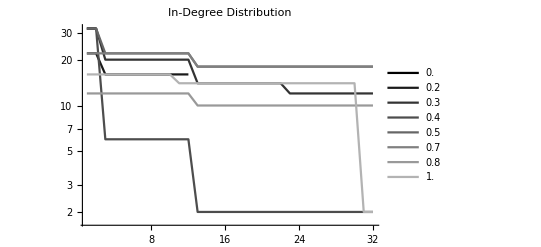
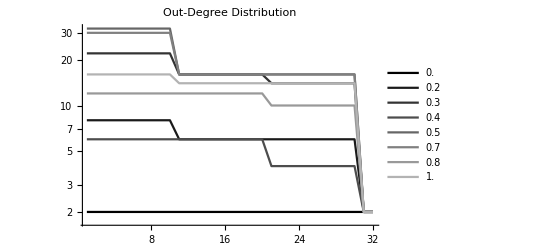
{WIDTH = 3,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 4,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 5,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 6,-Graphics-,-Graphics-,-Graphics-}
{WIDTH = 7,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[

lines=
DeleteCases[Table[

width=k;
timesteps=2^width;
ics=Tuples[{0,1},width];
rules=Range[0,255];

rr=DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^width,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null];

If[rr≠{},
icsw=Tuples[{0,1},width];
steps=
Flatten[Table[Table[CellularAutomaton[rr[[j]],icsw[[i]],1],{i,1,Length[icsw]}],{j,1,Length[rr]}],1]//DeleteDuplicates;
f[x_]:=x[[1]]->x[[2]];
g=f/@steps;
{VertexInDegree[Graph[g]]//Sort//Reverse,VertexOutDegree[Graph[g]]//Sort//Reverse,(VertexInDegree[Graph[g]]/VertexOutDegree[Graph[g]])//Sort//Reverse,p}
]

,{p,0.0,1,0.1}]
,Null];


f[x_]:=x[[2]];
h[x_]:=x[[3]];
in=ListLogPlot[First/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"In-Degree Distribution"];
out=ListLogPlot[f/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"Out-Degree Distribution"];
inout=ListLogPlot[h/@lines,PlotRange->All,Joined->True,PlotLegends->Last/@lines,PlotStyle->Table[GrayLevel[i],{i,0,1,0.1}],PlotLabel->"In/Out-Degree Distribution"];
{"WIDTH = "<>ToString[k],in,out,inout}

,{k,3,7}]//Column
```

### Distribution of Reversable Rules per Width

Looks good!

```mathematica
rrs=
Table[
Table[

widthca=k;
timesteps=2^widthca;
ics=Tuples[{0,1},widthca];
rules=Range[0,255];

DeleteCases[Table[
If[
Round[(Table[CellularAutomaton[rules[[i]],ics[[j]],1]//Last,{j,1,Length[ics]}]//Gather//Length)/ 2^widthca,0.1]==p,
rules[[i]]
]
,{i,1,Length[rules]}],Null]//Length

,{k,3,7}]
,{p,0,1,0.1}]
```

{{0,0,2,2,2},{2,2,0,0,8},{14,6,8,20,28},{0,8,30,24,8},{0,40,8,8,40},{60,36,66,72,26},{108,48,0,72,100},{0,56,106,36,20},{0,48,20,8,8},{36,4,0,8,0},{36,8,16,6,16}}

```mathematica
PieChart[rrs//Transpose,ChartLegends->Table[p,{p,0,1,0.1}],ChartLabels->{Range[3,7],None}, SectorSpacing->0.6]
```

-Graphics-

### Explore Some Trajectories

Longest trajectories possible
Graph widths, cetrality, diameter and stuff, connectedness